```mathematica
FourierShift[x_]:=ResourceFunction["FourierShift"][x]
```

```mathematica
Clear[n,L,dx,dt,x,k,u,U1,U2,unew,ustar,unews,uhat,uhats,udot,T]
n=256;
L=20;
T=1.35264;
cfl=0.1;
dx = L/n;
dt = cfl*dx;
x = Table[-L/2+i*dx,{i,1,n}];
k = Table[-n/2+i-1,{i,1,n}];
(*Initial condition: u(x,0)=sech^2(x)*)
u =Sech[x]^2;
fExp = ⅇ^(ⅈ*k^3*dt/2);
```

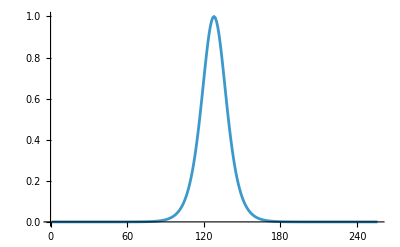

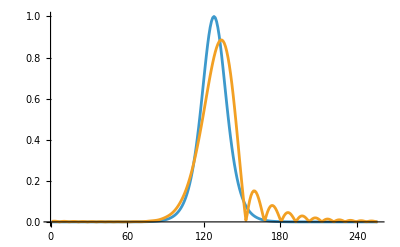

```mathematica
ListLinePlot[Abs[Re[u]],PlotRange->All]
uhat = Chop[FourierShift[Fourier[u]],10^-8]*fExp;
ustar=InverseFourier[uhat];
ustar = ustar + 3*cfl*ustar (RotateLeft[ustar]-RotateRight[ustar]);
uhat = Chop[FourierShift[Fourier[u]],10^-8]*fExp;
udot=InverseFourier[uhat];
ListLinePlot[{Abs[Re[u]],Abs[Re[udot]]},PlotRange->All]
```

```mathematica
tSteps =Round[T/dt]; 
For[i=1,i<=tSteps,i++,uhat = FourierShift[Fourier[udot]]*fExp;
ustar=InverseFourier[uhat];
ustar = ustar + 3*cfl*ustar (RotateLeft[ustar]-RotateRight[ustar]);
uhat = FourierShift[Fourier[u]]*fExp;
udot=InverseFourier[uhat]]
ListLinePlot[{Re[u],Abs[Re[udot]]},PlotRange->All]
```

-Graphics-